# b = 4 LRW Fractal Dimension on 3d square Lattice

## myMantissaExponent[]

```mathematica
myMantissaExponent[expr_]:=Module[{mant,exp},
{mant,exp}=MantissaExponent[expr];
mant*=10;exp-=1;
{mant,exp}
]
```

## With all the points from the CLUSTER: “b=4.000000-LRW-3d-square-lattice-data-3-201.csv” TO 501 almost

### Raw data

```mathematica
data1=DeleteCases[Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b4LRW\\b=4.000000-LRW-3d-square-lattice-data-3-201.csv"}],"CSV"],2],{}];
```

```mathematica
data2=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b4LRW\\b=4.000000-LRW-3d-square-lattice-data-203-401.csv"}],"CSV"],2];
```

```mathematica
data3=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b4LRW\\b=4.000000-LRW-3d-square-lattice-data-403-501.csv"}],"CSV"],2];
```

```mathematica
(*data4=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b4LRW\\b=4.000000-LRW-3d-square-lattice-data-403-501.csv"}],"CSV"],2];*)
```

```mathematica
rawData=joinedData=Join[data1,data2,data3(*,data4*)];
```

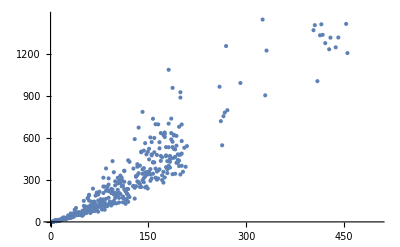

```mathematica
ListPlot[rawData]
```

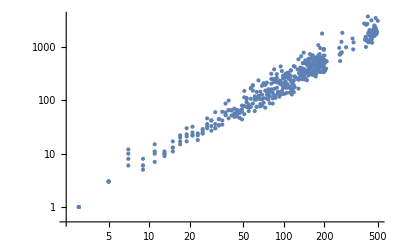

```mathematica
ListLogLogPlot[rawData]
```

```mathematica
Clear[x]
```

```mathematica
FindFit[Log[rawData],a+df *x,{a,df},x]
```

{a→-1.21851,df→1.42801}

```mathematica
lm=LinearModelFit[Log[rawData],x,x]
```

FittedModel[…]

```mathematica
lm["ParameterErrors"]
```

{0.0675623,0.0144462}

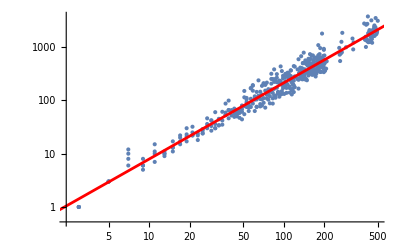

d_f=1.42801
Result from the litterature: UNKOWN

```mathematica
Show[ListLogLogPlot[rawData],
Plot[lm[x],{x,0,1000},PlotStyle->Red]
]
Print[ "d_f=",df/.FindFit[Log[rawData],a+df *x,{a,df},x],"
Result from the litterature: UNKOWN"]
```

### Drop the first few

```mathematica
joinedData=rawData;
```

```mathematica
dropped=Drop[joinedData,5];
FindFit[Log[dropped],a+df *x,{a,df},x]
lm=LinearModelFit[Log[dropped],x,x]
```

{a→-1.15832,df→1.41564}

FittedModel[…]

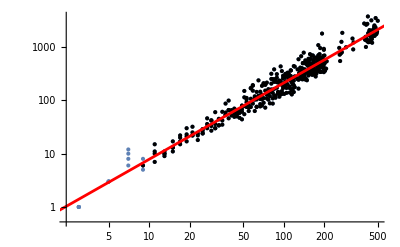

d_f=1.43155
Result from the litterature: UNKNOWN

```mathematica
dropped=Drop[Drop[joinedData,15],0];
lm=LinearModelFit[Log[dropped],x,x];
Show[ListLogLogPlot[joinedData],ListLogLogPlot[dropped,PlotStyle->Black],
Plot[lm[x],{x,0,1000},PlotStyle->Red]
]
Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"
Result from the litterature: UNKNOWN"]
```

```mathematica
lm["ParameterErrors"]
```

{0.0773985,0.0163788}

### Get stdDev by using Kay’s method

#### All the data

```mathematica
rawData=joinedData;
joinedData=rawData;
```

```mathematica
empirical=Module[{sampled,lm,a,df,x,slopeData,meanSlope,stdDevSlope},

slopeData=Table[
sampled=RandomSample[Log[joinedData],Floor[Length[joinedData]/2]];

lm=FindFit[sampled,a+df *x,{a,df},x];

df/.lm
,{i,1,10000}];

meanSlope=Mean[slopeData];
stdDevSlope=StandardDeviation [slopeData];

Return[{meanSlope,stdDevSlope}];
];
```

RandomSample::lrwl: The set of items to sample from, Log[rawData], should be a non-empty list or a rule weights -> choices.

FindFit::fitd: First argument RandomSample[Log[rawData],0] in FindFit is not a list or a rectangular array.

ReplaceAll::reps: {FindFit[RandomSample[Log[rawData],0],a$48284+df$48284 x$48284,{a$48284,df$48284},x$48284]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

RandomSample::lrwl: The set of items to sample from, Log[rawData], should be a non-empty list or a rule weights -> choices.

FindFit::fitd: First argument RandomSample[Log[rawData],0] in FindFit is not a list or a rectangular array.

ReplaceAll::reps: {FindFit[RandomSample[Log[rawData],0],a$48284+df$48284 x$48284,{a$48284,df$48284},x$48284]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

RandomSample::lrwl: The set of items to sample from, Log[rawData], should be a non-empty list or a rule weights -> choices.

General::stop: Further output of RandomSample::lrwl will be suppressed during this calculation.

FindFit::fitd: First argument RandomSample[Log[rawData],0] in FindFit is not a list or a rectangular array.

General::stop: Further output of FindFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[RandomSample[Log[rawData],0],a$48284+df$48284 x$48284,{a$48284,df$48284},x$48284]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Return[{df$48284/.FindFit[RandomSample[Log[rawData],0],a$48284+df$48284 x$48284,{a$48284,df$48284},x$48284],0}]

```mathematica
empirical
```

{df$48284/.FindFit[RandomSample[Log[rawData],0],a$48284+df$48284 x$48284,{a$48284,df$48284},x$48284],0}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x];
lm["ParameterErrors"]
{meanExact,stdDevExact}={(lm["ParameterTable"]//Normal)[[1,3,2]],lm["ParameterErrors"][[2]]}
dfExact=df/.FindFit[joinedData,a+df *x,{a,df},x]
{mantExact,expExact}=myMantissaExponent[meanExact]
{mantstdDevExact,expstdDevExact}=MantissaExponent[stdDevExact]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[Log[rawData],x,x][ParameterErrors]

Part::partd: Part specification LinearModelFit[Log[rawData],x,x][ParameterTable]⟦1,3,2⟧ is longer than depth of object.

Part::partw: Part 2 of LinearModelFit[Log[rawData],x,x][ParameterErrors] does not exist.

{LinearModelFit[Log[rawData],x,x][ParameterTable]⟦1,3,2⟧,LinearModelFit[Log[rawData],x,x][ParameterErrors]⟦2⟧}

FindFit::fitd: First argument rawData in FindFit is not a list or a rectangular array.

ReplaceAll::reps: {FindFit[rawData,a+df x,{a,df},x]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

df/.FindFit[rawData,a+df x,{a,df},x]

Set::shape: Lists {mant$48366,exp$48366} and MantissaExponent[LinearModelFit[Log[rawData],x,x][ParameterTable]⟦1,3,2⟧] are not the same shape.

TimesBy::rvalue: mant$48366 is not a variable with a value, so its value cannot be changed.

SubtractFrom::rvalue: exp$48366 is not a variable with a value, so its value cannot be changed.

{mant$48366,exp$48366}

Set::shape: Lists {mantstdDevExact,expstdDevExact} and MantissaExponent[LinearModelFit[Log[rawData],x,x][ParameterErrors]⟦2⟧] are not the same shape.

MantissaExponent[LinearModelFit[Log[rawData],x,x][ParameterErrors]⟦2⟧]

```mathematica
{mantEmp,expEmp}=myMantissaExponent[empirical[[1]]]
```

Set::shape: Lists {mant$48405,exp$48405} and MantissaExponent[df$48284/.FindFit[RandomSample[Log[rawData],0],a$48284+df$48284 x$48284,{a$48284,df$48284},x$48284]] are not the same shape.

TimesBy::rvalue: mant$48405 is not a variable with a value, so its value cannot be changed.

SubtractFrom::rvalue: exp$48405 is not a variable with a value, so its value cannot be changed.

{mant$48405,exp$48405}

```mathematica
Print[" The exact value of the slope from the data is (",mantExact,"±",mantstdDevExact,")×",Superscript[10,MantissaExponent[meanExact][[2]]-1], "
 While, by using Kay's procedure, we get (",mantEmp,"±",MantissaExponent[empirical[[2]]][[1]],")×",Superscript[10,expEmp]]
```

Part::partw: Part 2 of MantissaExponent[LinearModelFit[Log[rawData],x,x][ParameterTable]⟦1,3,2⟧] does not exist.

The exact value of the slope from the data is (mant$48366±mantstdDevExact)×10^(-1+MantissaExponent[LinearModelFit[Log[rawData],x,x][ParameterTable]⟦1,3,2⟧]⟦2⟧)
 While, by using Kay's procedure, we get (mant$48405±0)×10^exp$48405

#### On dropped data

```mathematica
joinedData=dropped=Drop[rawData,15];
```

Drop::normal: Nonatomic expression expected at position 1 in Drop[rawData,15].

```mathematica
empirical=Module[{sampled,lm,a,df,x,slopeData,meanSlope,stdDevSlope},

slopeData=Table[
sampled=RandomSample[Log[joinedData],Floor[Length[joinedData]/2]];

lm=FindFit[sampled,a+df *x,{a,df},x];

df/.lm
,{i,1,10000}];

meanSlope=Mean[slopeData];
stdDevSlope=StandardDeviation [slopeData];

Return[{meanSlope,stdDevSlope}];
];
```

RandomSample::lrwl: The set of items to sample from, Log[Drop[rawData,15]], should be a non-empty list or a rule weights -> choices.

FindFit::fitd: First argument RandomSample[Log[Drop[rawData,15]],1] in FindFit is not a list or a rectangular array.

ReplaceAll::reps: {FindFit[RandomSample[Log[Drop[rawData,15]],1],a$48426+df$48426 x$48426,{a$48426,df$48426},x$48426]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

RandomSample::lrwl: The set of items to sample from, Log[Drop[rawData,15]], should be a non-empty list or a rule weights -> choices.

FindFit::fitd: First argument RandomSample[Log[Drop[rawData,15]],1] in FindFit is not a list or a rectangular array.

ReplaceAll::reps: {FindFit[RandomSample[Log[Drop[rawData,15]],1],a$48426+df$48426 x$48426,{a$48426,df$48426},x$48426]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

RandomSample::lrwl: The set of items to sample from, Log[Drop[rawData,15]], should be a non-empty list or a rule weights -> choices.

General::stop: Further output of RandomSample::lrwl will be suppressed during this calculation.

FindFit::fitd: First argument RandomSample[Log[Drop[rawData,15]],1] in FindFit is not a list or a rectangular array.

General::stop: Further output of FindFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[RandomSample[Log[Drop[rawData,15]],1],a$48426+df$48426 x$48426,{a$48426,df$48426},x$48426]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Return[{df$48426/.FindFit[RandomSample[Log[Drop[rawData,15]],1],a$48426+df$48426 x$48426,{a$48426,df$48426},x$48426],0}]

```mathematica
empirical
```

{df$48426/.FindFit[RandomSample[Log[Drop[rawData,15]],1],a$48426+df$48426 x$48426,{a$48426,df$48426},x$48426],0}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x];
lm["ParameterErrors"]
{meanExact,stdDevExact}={(lm["ParameterTable"]//Normal)[[1,3,2]],lm["ParameterErrors"][[2]]}
dfExact=df/.FindFit[joinedData,a+df *x,{a,df},x]
{mantExact,expExact}=myMantissaExponent[meanExact]
{mantstdDevExact,expstdDevExact}=MantissaExponent[stdDevExact]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[Log[Drop[rawData,15]],x,x][ParameterErrors]

Part::partd: Part specification LinearModelFit[Log[Drop[rawData,15]],x,x][ParameterTable]⟦1,3,2⟧ is longer than depth of object.

Part::partw: Part 2 of LinearModelFit[Log[Drop[rawData,15]],x,x][ParameterErrors] does not exist.

{LinearModelFit[Log[Drop[rawData,15]],x,x][ParameterTable]⟦1,3,2⟧,LinearModelFit[Log[Drop[rawData,15]],x,x][ParameterErrors]⟦2⟧}

FindFit::fitd: First argument Drop[rawData,15] in FindFit is not a list or a rectangular array.

ReplaceAll::reps: {FindFit[Drop[rawData,15],a+df x,{a,df},x]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

df/.FindFit[Drop[rawData,15],a+df x,{a,df},x]

Set::shape: Lists {mant$49641,exp$49641} and MantissaExponent[LinearModelFit[Log[Drop[rawData,15]],x,x][ParameterTable]⟦1,3,2⟧] are not the same shape.

TimesBy::rvalue: mant$49641 is not a variable with a value, so its value cannot be changed.

SubtractFrom::rvalue: exp$49641 is not a variable with a value, so its value cannot be changed.

{mant$49641,exp$49641}

Set::shape: Lists {mantstdDevExact,expstdDevExact} and MantissaExponent[LinearModelFit[Log[Drop[rawData,15]],x,x][ParameterErrors]⟦2⟧] are not the same shape.

MantissaExponent[LinearModelFit[Log[Drop[rawData,15]],x,x][ParameterErrors]⟦2⟧]

```mathematica
{mantEmp,expEmp}=myMantissaExponent[empirical[[1]]]
```

Set::shape: Lists {mant$49662,exp$49662} and MantissaExponent[df$48426/.FindFit[RandomSample[Log[Drop[rawData,15]],1],a$48426+df$48426 x$48426,{a$48426,df$48426},x$48426]] are not the same shape.

TimesBy::rvalue: mant$49662 is not a variable with a value, so its value cannot be changed.

SubtractFrom::rvalue: exp$49662 is not a variable with a value, so its value cannot be changed.

{mant$49662,exp$49662}

```mathematica
Print[" The exact value of the slope from the data is (",mantExact,"±",mantstdDevExact,")×",Superscript[10,MantissaExponent[meanExact][[2]]-1], "
 While, by using Kay's procedure, we get (",mantEmp,"±",MantissaExponent[empirical[[2]]][[1]],")×",Superscript[10,expEmp]]
```

Part::partw: Part 2 of MantissaExponent[LinearModelFit[Log[Drop[rawData,15]],x,x][ParameterTable]⟦1,3,2⟧] does not exist.

The exact value of the slope from the data is (mant$49641±mantstdDevExact)×10^(-1+MantissaExponent[LinearModelFit[Log[Drop[rawData,15]],x,x][ParameterTable]⟦1,3,2⟧]⟦2⟧)
 While, by using Kay's procedure, we get (mant$49662±0)×10^exp$49662